```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/INI/MMB paper/figures/abba

```mathematica
kabon=10
kaboff=0.05
kbbon=8
kbboff=0.03
volume=1000000
maxtime=20
a0=10000
b0=10000
```

10

0.05

8

0.03

1000000

20

10000

10000

```mathematica
(* Everything below here should take care of itself *)
```

```mathematica
(* Load and look at data *)
```

```mathematica
simdata=Import["abbaout.txt","CSV"];
```

```mathematica
simdata;
```

```mathematica
plotdata=Table[Table[{simdata[[row,1]],simdata[[row,col]]},{row,Length[simdata]}],{col,2,Length[simdata[[1]]]}];
```

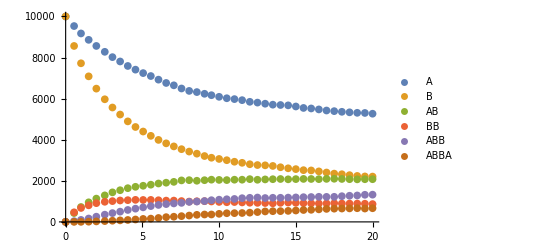

```mathematica
ListPlot[plotdata,PlotLegends->{"A","B","AB","BB","ABB","ABBA"}]
```

```mathematica
kabonv=N[kabon/volume]
kaboffv=N[kaboff]
kbbonv=N[kbbon/volume]
kbboffv=N[kbboff]
```

0.00001

0.05

8.×10^-6

0.03

```mathematica
eqa=a'[t]==kaboffv*ab[t]+kaboffv*abb[t]+2*kaboffv*abba[t]-kabonv*a[t]*(b[t]+2*bb[t]+abb[t])
```

a'[t]==0.05 ab[t]+0.05 abb[t]+0.1 abba[t]-0.00001 a[t] (abb[t]+b[t]+2 bb[t])

```mathematica
eqb=b'[t]==kaboffv*ab[t]+kbboffv*abb[t]+2*kbboffv*bb[t]-b[t]*(kabonv*a[t]+kbbonv*ab[t]+2*kbbonv*b[t])
```

b'[t]==0.05 ab[t]+0.03 abb[t]-(0.00001 a[t]+8.×10^-6 ab[t]+0.000016 b[t]) b[t]+0.06 bb[t]

```mathematica
eqab=ab'[t]==kabonv*a[t]*b[t]+kbboffv*abb[t]+2*kbboffv*abba[t]-ab[t]*(kaboffv+kbbonv*b[t]+2*kbbonv*ab[t])
```

ab'[t]==0.03 abb[t]+0.06 abba[t]-ab[t] (0.05+0.000016 ab[t]+8.×10^-6 b[t])+0.00001 a[t] b[t]

```mathematica
eqbb=bb'[t]==kbbonv*b[t]*b[t]+kaboffv*abb[t]-bb[t]*(kbboffv+2*kabonv*a[t])
```

bb'[t]==0.05 abb[t]+8.×10^-6 b[t]^2-(0.03+0.00002 a[t]) bb[t]

```mathematica
eqabb=abb'[t]==kbbonv*ab[t]*b[t]+2*kaboffv*abba[t]+2*kabonv*a[t]*bb[t]-abb[t]*(kbboffv+kabonv*a[t]+kaboffv)
```

abb'[t]==-(0.08+0.00001 a[t]) abb[t]+0.1 abba[t]+8.×10^-6 ab[t] b[t]+0.00002 a[t] bb[t]

```mathematica
eqabba=abba'[t]==kabonv*a[t]*abb[t]+kbbonv*ab[t]*ab[t]-abba[t]*(2*kaboffv+kbboffv)
```

abba'[t]==8.×10^-6 ab[t]^2+0.00001 a[t] abb[t]-0.13 abba[t]

```mathematica
soln=NDSolve[{eqa,eqb,eqab,eqbb,eqabb,eqabba,a[0]==a0,b[0]==b0,ab[0]==0,bb[0]==0,abb[0]==0,abba[0]==0},{a,b,ab,bb,abb,abba},{t,0,maxtime}];
```

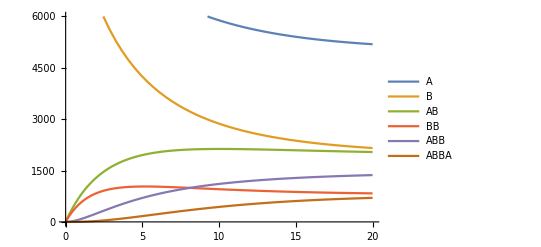

```mathematica
Plot[Evaluate[{a[t],b[t],ab[t],bb[t],abb[t],abba[t]}/.soln],{t,0,maxtime},PlotLegends->{"A","B","AB","BB","ABB","ABBA"},PlotRange->{0,6000}]
```

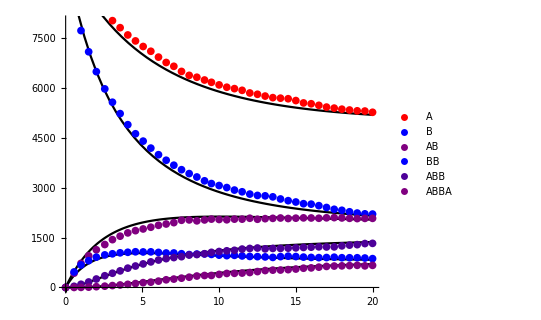

```mathematica
Show[{Plot[Evaluate[{a[t],b[t],ab[t],bb[t],abb[t],abba[t]}/.soln],{t,0,maxtime},PlotStyle->Black],
ListPlot[plotdata,PlotStyle->{Red,Blue,RGBColor[0.5,0,0.5],Blue,RGBColor[0.3,0,0.6],RGBColor[0.5,0,0.5]},PlotLegends->{"A","B","AB","BB","ABB","ABBA"}]},PlotRange->{0,8000},AspectRatio->0.8,AxesStyle->Bold]
```